```mathematica
ClearAll[c,G,MSun,rhoRadBBN];

c=29979245800;                   (*velocidad de la luz:cm/s*)
G=66743/10^12;                   (*constante gravitacional:cm^3/(g s^2)*)
MSun=198847*10^28;               (*masa solar:g*)

rhoRadBBN=7331305019814086*10^11;
(*densidad de energía de radiación en BBN:erg/cm^3*)
```

```mathematica
ti=37/50;                       (*coordenada temporal de BBN:0.74 s*)
ai=83/500000000000;             (*factor de escala en BBN:1.66*10^-10*)
Hti=67/100;                     (*parámetro de Hubble en BBN:0.67 s^-1*)
```

```mathematica
ρ0[ξ_]:= ξ*rhoRadBBN
```

```mathematica
Cxi[ξ_]:= (4π G)/(3c^2)*ρ0[ξ]
```

```mathematica
ClearAll[sol];
```

```mathematica
tMin=-5;
(* n = -3 luego 
(Y[t])^((n-1)/2) ----> Y^-2
*)
```

```mathematica
ClearAll[sol,tBounce]
```

```mathematica
sol[ξ_]:=sol[ξ]=NDSolve[{Y'[t]==v[t],v'[t]==2*Cxi[ξ]*(Y[t])^(-2),Y[ti]==1,v[ti]==2*Hti},{Y,v},{t,tMin,ti},WorkingPrecision->40,AccuracyGoal->25,PrecisionGoal->25,
Method->"StiffnessSwitching",MaxSteps->Infinity ];
```

```mathematica
Yfunc[ξ_,t_]:=Y[t]/. sol[ξ][[1]];
vFunc[ξ_,t_]:=v[t]/. sol[ξ][[1]];
```

```mathematica
apos1[ξ_, t_] := ai*√Yfunc[ξ, t]
```

```mathematica
sol[1/10];
```

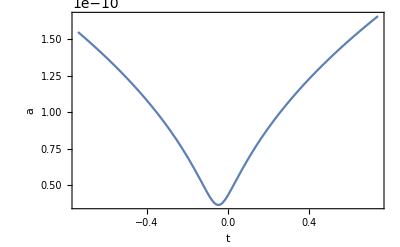

```mathematica
Plot[apos1[1/10, t], {t, -ti, ti}, AxesLabel->{t,a},Frame->True, PlotRangePadding->0 ]
```

```mathematica
ClearAll[tBounce]
```

```mathematica
tBounce[ξ_]:=tBounce[ξ]=t/. FindRoot[vFunc[ξ,t]==0,{t,0,-0.1},WorkingPrecision->40];
```

```mathematica
tB= tBounce[1/10]
```

-0.0474714961991318651644429953440325745702

```mathematica
apos[ξ_, t_]:=ai*Sqrt[Y[t+tBounce[ξ]]/. sol[ξ][[1]]];
```

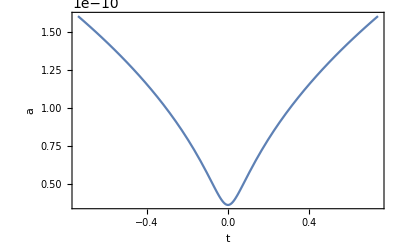

```mathematica
Plot[apos[1/10, t], {t, -ti, ti}, AxesLabel->{t,a},Frame->True, PlotRangePadding->0 ]
```

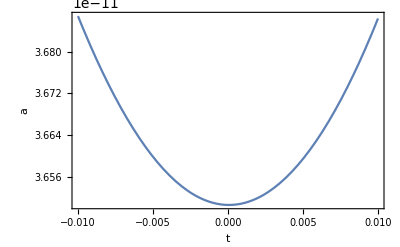

```mathematica
Plot[apos[1/10, t], {t, -1/100, 1/100}, AxesLabel->{t,a},Frame->True, PlotRangePadding->0 ]
```

```mathematica
ar := ai/ti^(1/2)
aRad[t_]:= ar*t^(1/2)
```

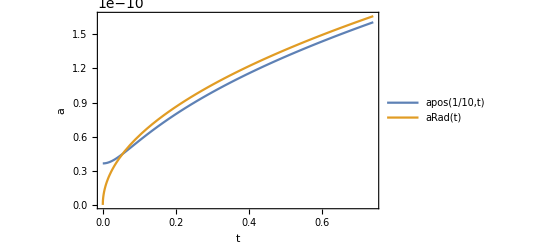

```mathematica
Plot[{apos[1/10, t],aRad[t]},{t,0,ti},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0, PlotLegends->"Expressions"]
```

```mathematica
ρbh[ξ_,t_]:= ρ0[ξ]*(ai/apos[ξ, t])^4
```

```mathematica
Plot[ρbh[1/10, t],{t,-ti,ti},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0]
```

-Graphics-

```mathematica
ρbh[1/10,0]
```

3.13408423420499247100802113758438517522×10^28

```mathematica
ρbh[1/10, 10^(-4)]
```

3.13408727542579823632487173483063258132×10^28

```mathematica
DotA[ξ_, t_] := (ai^2*vFunc[ξ, t+tBounce[ξ]])/(2*apos[ξ, t])
```

```mathematica
DotA[1/10, 0]
```

0.

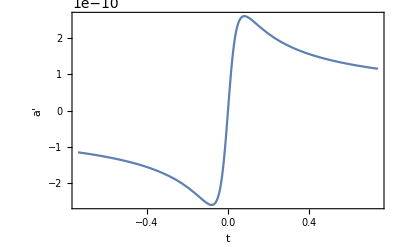

```mathematica
Plot[DotA[1/10, t],{t,-ti,ti},AxesLabel->{"t","a'"},Frame->True,PlotRangePadding->0]
```

```mathematica
DDotA[ξ_?NumericQ,t_?NumericQ]:=(DotA[ξ,t+10^-6]-DotA[ξ,t-10^-6])/(2*10^-6)
```

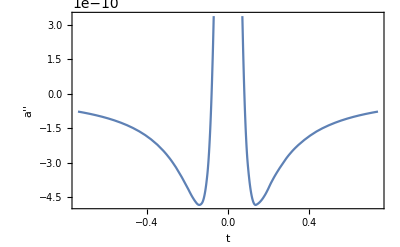

```mathematica
Plot[DDotA[1/10, t],{t,-ti,ti},AxesLabel->{"t","a''"},Frame->True,PlotRangePadding->0]
```

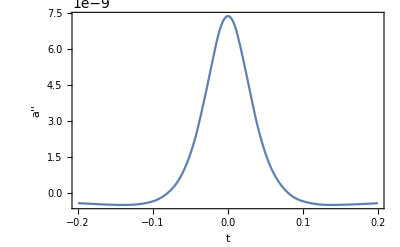

```mathematica
Plot[DDotA[1/10, t],{t,-0.2,0.2},AxesLabel->{"t","a''"},Frame->True,PlotRangePadding->0]
```

```mathematica
FindRoot[DDotA[1/10,t]==0,{t,0.1}]
```

{t→0.0807196}

```mathematica
DDotA[1/10,0.08071964627867803]
```

0.

```mathematica
ρrad[ξ_, t_]:= (3c^2)/(8π G)(DotA[ξ, t]/apos[ξ, t])^2 -ρbh[ξ, t]
```

```mathematica
Plot[ρrad[1/10, t],{t,-ti, ti},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0]
```

-Graphics-

```mathematica
ρrad[1/10, 10^(-4)]
```

-3.13402202965685094234694810180879866977×10^28

```mathematica
ρrad[1/10, 0]
```

-3.13408423420499247100802113758438517522×10^28

```mathematica
Plot[ρrad[1/10, t],{t,-1/10,1/10},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0]
```

-Graphics-

```mathematica
FindRoot[ρrad[1/10,t]==0,{t,0.03}]
```

{t→0.0234804}

```mathematica
HubbleParameter[ξ_, t_]:= √((8π G)/(3c^2)(ρrad[ξ, t]+ρbh[ξ, t]))
```

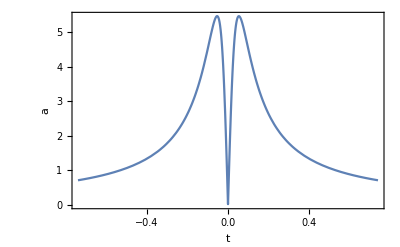

```mathematica
Plot[HubbleParameter[1/10, t],{t,-ti,ti},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0]
```

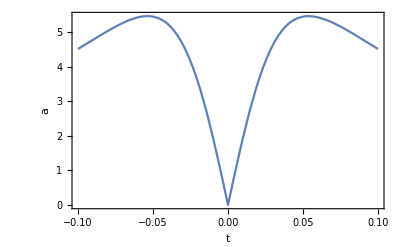

```mathematica
Plot[HubbleParameter[1/10, t],{t,-1/10,1/10},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0]
```

```mathematica
HubbleParameter[1/10, 0]
```

0.

```mathematica
Plot[ρrad[1/10, t]+ρbh[1/10, t],{t,-1/10,1/10},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0]
```

-Graphics-

```mathematica
FindMaximum[ρrad[1/10,t],{t,0.05},WorkingPrecision->30]
```

{3.54248854831275489514984132487×10^28,{t→0.0631103396217590597134182254972}}

```mathematica
HubbleParameter[1/10, 10^(-4)]
```

0.02014733641803988333233288156345798

```mathematica
0.0201473364180398833323328815634579829361538265815805592297`34.586149904901504/5000
```

4.029467283607976666466576312691597×10^-6

```mathematica
MHubble[ξ_, t_]:= (4π c)/3*(ρrad[ξ, t]+ρbh[ξ, t])/(HubbleParameter[ξ, t])^3
```

```mathematica
Plot[MHubble[1/10, t],{t,-10^(-7),10^(-7)},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0]
```

-Graphics-

```mathematica
γ := 0.2
Minic[ξ_, t_] := γ*MHubble[ξ, t]
```

```mathematica
Minic[1/10, 10^(-4)]
```

2.00373×10^39

```mathematica
Minic[1/10,10^(-4)]/MSun
```

1.00767×10^6

```mathematica
β = ρbh[1/10, 10^(-4)]/(ρrad[1/10, 10^(-4)]+ρbh[1/10, 10^(-4)])
```

48035.10367020944255875820962626648